```mathematica
CompFromPart[count_,part_]:=Block[{result={}, g=CompleteGraph[count],current=0,vertices},
vertices=VertexList[g];
Table[
result=Append[result,EdgeList[VertexDelete[g,Take[vertices,p-Length[vertices]]]]];
g=VertexDelete[g,Take[vertices,p]];
vertices=Take[vertices,p-Length[vertices]];
,
{p,part}
];
result
]
```

```mathematica
ListSols2[count_]:=Block[{parts=Map[Reverse,IntegerPartitions[count,{4}]], comp,g},
Table[
comp=Flatten[CompFromPart[count,part]];
g=CompleteGraph[count];
Labeled[
CompleteGraph[count,
GraphLayout->"RadialEmbedding",
EdgeStyle->Map[#->{Thick,Red}&,comp],
EdgeLabels->{First[EdgeList[g]]->Style[Framed[Length[comp],Background->White],Darker[Green],Bold,14],
Last[EdgeList[g]]->Style[Framed[EdgeCount[g],Background->White],Blue,Bold,14]},
VertexStyle->Red,
VertexLabels->"Name"
],
Reverse[part]]
,
{part, parts}
]
]
```

```mathematica
Table[Count[IntegerPartitions[n],{4,___}],{n,0,60}]
```

{0,0,0,0,1,1,2,3,5,6,9,11,15,18,23,27,34,39,47,54,64,72,84,94,108,120,136,150,169,185,206,225,249,270,297,321,351,378,411,441,478,511,551,588,632,672,720,764,816,864,920,972,1033,1089,1154,1215,1285,1350,1425,1495,1575}

```mathematica
Table[Length[IntegerPartitions[n,{4}]],{n,0,60}]
```

{0,0,0,0,1,1,2,3,5,6,9,11,15,18,23,27,34,39,47,54,64,72,84,94,108,120,136,150,169,185,206,225,249,270,297,321,351,378,411,441,478,511,551,588,632,672,720,764,816,864,920,972,1033,1089,1154,1215,1285,1350,1425,1495,1575}

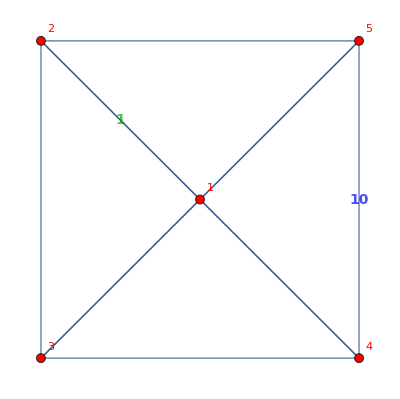
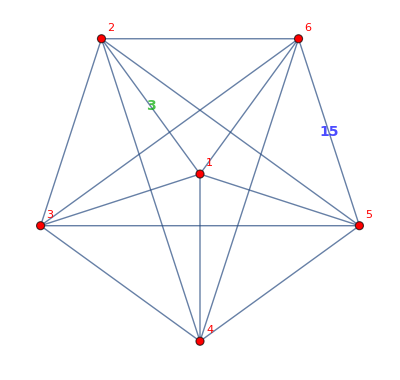
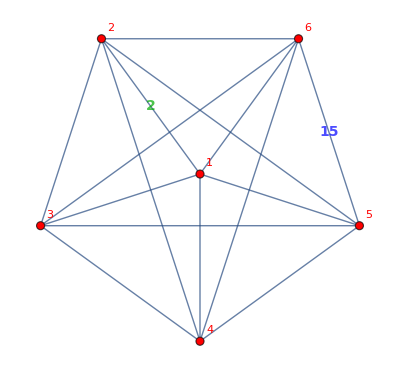
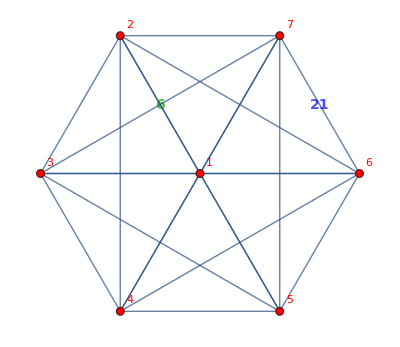
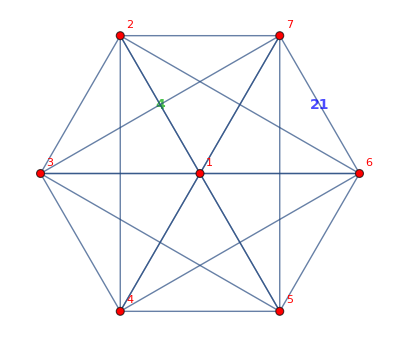
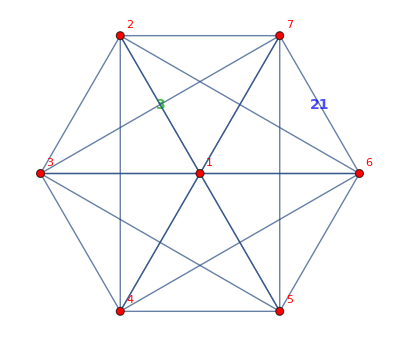
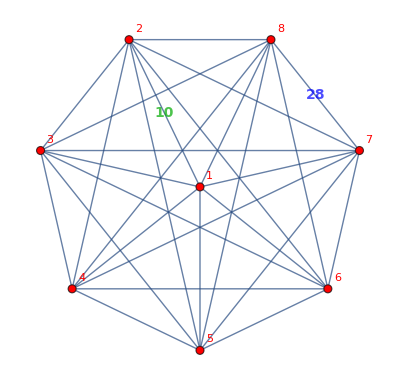
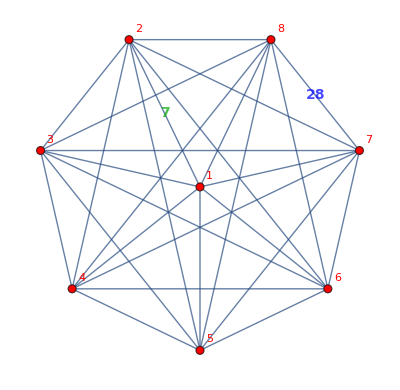
51→{-Graphics-{2,1,1,1}}
62→{-Graphics-{3,1,1,1},-Graphics-{2,2,1,1}}
73→{-Graphics-{4,1,1,1},-Graphics-{3,2,1,1},-Graphics-{2,2,2,1}}
85→{-Graphics-{5,1,1,1},-Graphics-{4,2,1,1},-Graphics-{3,3,1,1},-Graphics-{3,2,2,1},-Graphics-{2,2,2,2}}
96→{-Graphics-{6,1,1,1},-Graphics-{5,2,1,1},-Graphics-{4,3,1,1},-Graphics-{4,2,2,1},-Graphics-{3,3,2,1},-Graphics-{3,2,2,2}}
109→{-Graphics-{7,1,1,1},-Graphics-{6,2,1,1},-Graphics-{5,3,1,1},-Graphics-{5,2,2,1},-Graphics-{4,4,1,1},-Graphics-{4,3,2,1},-Graphics-{4,2,2,2},-Graphics-{3,3,3,1},-Graphics-{3,3,2,2}}
1111→{-Graphics-{8,1,1,1},-Graphics-{7,2,1,1},-Graphics-{6,3,1,1},-Graphics-{6,2,2,1},-Graphics-{5,4,1,1},-Graphics-{5,3,2,1},-Graphics-{5,2,2,2},-Graphics-{4,4,2,1},-Graphics-{4,3,3,1},-Graphics-{4,3,2,2},-Graphics-{3,3,3,2}}
1215→{-Graphics-{9,1,1,1},-Graphics-{8,2,1,1},-Graphics-{7,3,1,1},-Graphics-{7,2,2,1},-Graphics-{6,4,1,1},-Graphics-{6,3,2,1},-Graphics-{6,2,2,2},-Graphics-{5,5,1,1},-Graphics-{5,4,2,1},-Graphics-{5,3,3,1},-Graphics-{5,3,2,2},-Graphics-{4,4,3,1},-Graphics-{4,4,2,2},-Graphics-{4,3,3,2},-Graphics-{3,3,3,3}}

```mathematica
Column[
Table[
With[{sol=ListSols2[max]},Labeled[Framed[max],Style[Length[sol],24,Black,Background->Yellow]]->sol],
{max,5,12}
]
]
```